Sphere sphere collision

```mathematica
Clear["*"];
Subscript[p, 1]={Subscript[p, 1x],Subscript[p, 1y],Subscript[p, 1z]};
Subscript[v, 1]={Subscript[v, 1x],Subscript[v, 1y],Subscript[v, 1z]};
Subscript[r, 1];
Subscript[p, 2]={Subscript[p, 2x],Subscript[p, 2y],Subscript[p, 2z]};
Subscript[v, 2]={Subscript[v, 2x],Subscript[v, 2y],Subscript[v, 2z]};
Subscript[r, 2];
(Subscript[p, 1]+Subscript[v, 1] t)-(Subscript[p, 2]+Subscript[v, 2] t)
```

{p_x-p_(2 x)+t v_x-t v_(2 x),p_y-p_(2 y)+t v_y-t v_(2 y),p_z-p_(2 z)+t v_z-t v_(2 z)}

```mathematica
{Subscript[p, x]-Subscript[p, 2 x]-0.5 Subscript[v, x]+0.5 Subscript[v, 2 x],Subscript[p, y]-Subscript[p, 2 y]-0.5 Subscript[v, y]+0.5 Subscript[v, 2 y],Subscript[p, z]-Subscript[p, 2 z]-0.5 Subscript[v, z]+0.5 Subscript[v, 2 z]}
```

{ (p_x-p_(2 x)-0.5 v_x+0.5 v_(2 x)), (p_y-p_(2 y)-0.5 v_y+0.5 v_(2 y)), (p_z-p_(2 z)-0.5 v_z+0.5 v_(2 z))}

```mathematica
EuclideanDistance[{0,0,0},(Subscript[p, 1]+Subscript[v, 1] t)-(Subscript[p, 2]+Subscript[v, 2] t)]==Subscript[r, 1]+Subscript[r, 2]
```

√(Abs[-p_x+p_(2 x)-t v_x+t v_(2 x)]^2+Abs[-p_y+p_(2 y)-t v_y+t v_(2 y)]^2+Abs[-p_z+p_(2 z)-t v_z+t v_(2 z)]^2)==2

```mathematica
√Total[((Subscript[p, 2]+Subscript[v, 2] t)-(Subscript[p, 1]+Subscript[v, 1] t))^2]==Subscript[r, 1]+Subscript[r, 2]
```

√((-p_x+p_(2 x)-t v_x+t v_(2 x))^2+(-p_y+p_(2 y)-t v_y+t v_(2 y))^2+(-p_z+p_(2 z)-t v_z+t v_(2 z))^2)==2

```mathematica
Solve[√Total[((Subscript[p, 2]+Subscript[v, 2] t)-(Subscript[p, 1]+Subscript[v, 1] t))^2]==Subscript[r, 1]+Subscript[r, 2],t]
```

{{t→(-2 p_x v_x+2 p_(2 x) v_x+2 p_x v_(2 x)-2 p_(2 x) v_(2 x)-2 p_y v_y+2 p_(2 y) v_y+2 p_y v_(2 y)-2 p_(2 y) v_(2 y)-2 p_z v_z+2 p_(2 z) v_z+2 p_z v_(2 z)-2 p_(2 z) v_(2 z)-√((2 p_x v_x-2 p_(2 x) v_x-2 p_x v_(2 x)+2 p_(2 x) v_(2 x)+2 p_y v_y-2 p_(2 y) v_y-2 p_y v_(2 y)+2 p_(2 y) v_(2 y)+2 p_z v_z-2 p_(2 z) v_z-2 p_z v_(2 z)+2 p_(2 z) v_(2 z))^2-4 (-4+p_x^2-2 p_x p_(2 x)+p_(2 x)^2+p_y^2-2 p_y p_(2 y)+p_(2 y)^2+p_z^2-2 p_z p_(2 z)+p_(2 z)^2) (v_x^2-2 v_x v_(2 x)+v_(2 x)^2+v_y^2-2 v_y v_(2 y)+v_(2 y)^2+v_z^2-2 v_z v_(2 z)+v_(2 z)^2)))/(2 (v_x^2-2 v_x v_(2 x)+v_(2 x)^2+v_y^2-2 v_y v_(2 y)+v_(2 y)^2+v_z^2-2 v_z v_(2 z)+v_(2 z)^2))},{t→(-2 p_x v_x+2 p_(2 x) v_x+2 p_x v_(2 x)-2 p_(2 x) v_(2 x)-2 p_y v_y+2 p_(2 y) v_y+2 p_y v_(2 y)-2 p_(2 y) v_(2 y)-2 p_z v_z+2 p_(2 z) v_z+2 p_z v_(2 z)-2 p_(2 z) v_(2 z)+√((2 p_x v_x-2 p_(2 x) v_x-2 p_x v_(2 x)+2 p_(2 x) v_(2 x)+2 p_y v_y-2 p_(2 y) v_y-2 p_y v_(2 y)+2 p_(2 y) v_(2 y)+2 p_z v_z-2 p_(2 z) v_z-2 p_z v_(2 z)+2 p_(2 z) v_(2 z))^2-4 (-4+p_x^2-2 p_x p_(2 x)+p_(2 x)^2+p_y^2-2 p_y p_(2 y)+p_(2 y)^2+p_z^2-2 p_z p_(2 z)+p_(2 z)^2) (v_x^2-2 v_x v_(2 x)+v_(2 x)^2+v_y^2-2 v_y v_(2 y)+v_(2 y)^2+v_z^2-2 v_z v_(2 z)+v_(2 z)^2)))/(2 (v_x^2-2 v_x v_(2 x)+v_(2 x)^2+v_y^2-2 v_y v_(2 y)+v_(2 y)^2+v_z^2-2 v_z v_(2 z)+v_(2 z)^2))}}

```mathematica
(√Total[((Subscript[p, 2]+Subscript[v, 2] t)-(Subscript[p, 1]+Subscript[v, 1] t))^2])^2==(Subscript[r, 1]+Subscript[r, 2])^2
```

(-p_x+p_(2 x)-t v_x+t v_(2 x))^2+(-p_y+p_(2 y)-t v_y+t v_(2 y))^2+(-p_z+p_(2 z)-t v_z+t v_(2 z))^2==4

```mathematica
Collect[(-Subscript[p, x]+Subscript[p, 2 x]-t Subscript[v, x]+t Subscript[v, 2 x])^2+(-Subscript[p, y]+Subscript[p, 2 y]-t Subscript[v, y]+t Subscript[v, 2 y])^2+(-Subscript[p, z]+Subscript[p, 2 z]-t Subscript[v, z]+t Subscript[v, 2 z])^2==(r1+r2)^2,t]
```

p_x^2-2 p_x p_(2 x)+p_(2 x)^2+p_y^2-2 p_y p_(2 y)+p_(2 y)^2+p_z^2-2 p_z p_(2 z)+p_(2 z)^2+t (2 p_x v_x-2 p_(2 x) v_x-2 p_x v_(2 x)+2 p_(2 x) v_(2 x)+2 p_y v_y-2 p_(2 y) v_y-2 p_y v_(2 y)+2 p_(2 y) v_(2 y)+2 p_z v_z-2 p_(2 z) v_z-2 p_z v_(2 z)+2 p_(2 z) v_(2 z))+t^2 (v_x^2-2 v_x v_(2 x)+v_(2 x)^2+v_y^2-2 v_y v_(2 y)+v_(2 y)^2+v_z^2-2 v_z v_(2 z)+v_(2 z)^2)==0

```mathematica
Subscript[p, x]^2-2 Subscript[p, x] Subscript[p, 2 x]+Subscript[p, 2 x]^2+Subscript[p, y]^2-2 Subscript[p, y] Subscript[p, 2 y]+Subscript[p, 2 y]^2+Subscript[p, z]^2-2 Subscript[p, z] Subscript[p, 2 z]+Subscript[p, 2 z]^2+t (2 Subscript[p, x] Subscript[v, x]-2 Subscript[p, 2 x] Subscript[v, x]-2 Subscript[p, x] Subscript[v, 2 x]+2 Subscript[p, 2 x] Subscript[v, 2 x]+2 Subscript[p, y] Subscript[v, y]-2 Subscript[p, 2 y] Subscript[v, y]-2 Subscript[p, y] Subscript[v, 2 y]+2 Subscript[p, 2 y] Subscript[v, 2 y]+2 Subscript[p, z] Subscript[v, z]-2 Subscript[p, 2 z] Subscript[v, z]-2 Subscript[p, z] Subscript[v, 2 z]+2 Subscript[p, 2 z] Subscript[v, 2 z])+t^2 (Subscript[v, x]^2-2 Subscript[v, x] Subscript[v, 2 x]+Subscript[v, 2 x]^2+Subscript[v, y]^2-2 Subscript[v, y] Subscript[v, 2 y]+Subscript[v, 2 y]^2+Subscript[v, z]^2-2 Subscript[v, z] Subscript[v, 2 z]+Subscript[v, 2 z]^2)-(r1+r2)^2==(r1+r2)^2-(r1+r2)^2
```

p_x^2-2 p_x p_(2 x)+p_(2 x)^2+p_y^2-2 p_y p_(2 y)+p_(2 y)^2+p_z^2-2 p_z p_(2 z)+p_(2 z)^2+t (2 p_x v_x-2 p_(2 x) v_x-2 p_x v_(2 x)+2 p_(2 x) v_(2 x)+2 p_y v_y-2 p_(2 y) v_y-2 p_y v_(2 y)+2 p_(2 y) v_(2 y)+2 p_z v_z-2 p_(2 z) v_z-2 p_z v_(2 z)+2 p_(2 z) v_(2 z))+t^2 (v_x^2-2 v_x v_(2 x)+v_(2 x)^2+v_y^2-2 v_y v_(2 y)+v_(2 y)^2+v_z^2-2 v_z v_(2 z)+v_(2 z)^2)==0

```mathematica
Total[Subscript[v, 1]^2]
```

v_x^2+v_y^2+v_z^2

```mathematica
-(r1+r2)^2+Subscript[p, x]^2-2 Subscript[p, x] Subscript[p, 2 x]+Subscript[p, 2 x]^2+Subscript[p, y]^2-2 Subscript[p, y] Subscript[p, 2 y]+Subscript[p, 2 y]^2+Subscript[p, z]^2-2 Subscript[p, z] Subscript[p, 2 z]+Subscript[p, 2 z]^2+t (2 Subscript[p, x] Subscript[v, x]-2 Subscript[p, 2 x] Subscript[v, x]-2 Subscript[p, x] Subscript[v, 2 x]+2 Subscript[p, 2 x] Subscript[v, 2 x]+2 Subscript[p, y] Subscript[v, y]-2 Subscript[p, 2 y] Subscript[v, y]-2 Subscript[p, y] Subscript[v, 2 y]+2 Subscript[p, 2 y] Subscript[v, 2 y]+2 Subscript[p, z] Subscript[v, z]-2 Subscript[p, 2 z] Subscript[v, z]-2 Subscript[p, z] Subscript[v, 2 z]+2 Subscript[p, 2 z] Subscript[v, 2 z])+t^2 (Total[Subscript[v, 1]^2]-2 Subscript[v, x] Subscript[v, 2 x]+Subscript[v, 2 x]^2-2 Subscript[v, y] Subscript[v, 2 y]+Subscript[v, 2 y]^2-2 Subscript[v, z] Subscript[v, 2 z]+Subscript[v, 2 z]^2)==0
```

p_x^2-2 p_x p_(2 x)+p_(2 x)^2+p_y^2-2 p_y p_(2 y)+p_(2 y)^2+p_z^2-2 p_z p_(2 z)+p_(2 z)^2+t (2 p_x v_x-2 p_(2 x) v_x-2 p_x v_(2 x)+2 p_(2 x) v_(2 x)+2 p_y v_y-2 p_(2 y) v_y-2 p_y v_(2 y)+2 p_(2 y) v_(2 y)+2 p_z v_z-2 p_(2 z) v_z-2 p_z v_(2 z)+2 p_(2 z) v_(2 z))+t^2 (v_x^2-2 v_x v_(2 x)+v_(2 x)^2+v_y^2-2 v_y v_(2 y)+v_(2 y)^2+v_z^2-2 v_z v_(2 z)+v_(2 z)^2)==0

```mathematica
Total[Subscript[v, 2]^2]
```

v_(2 x)^2+v_(2 y)^2+v_(2 z)^2

```mathematica
-(r1+r2)^2+Subscript[p, x]^2-2 Subscript[p, x] Subscript[p, 2 x]+Subscript[p, 2 x]^2+Subscript[p, y]^2-2 Subscript[p, y] Subscript[p, 2 y]+Subscript[p, 2 y]^2+Subscript[p, z]^2-2 Subscript[p, z] Subscript[p, 2 z]+Subscript[p, 2 z]^2+t (2 Subscript[p, x] Subscript[v, x]-2 Subscript[p, 2 x] Subscript[v, x]-2 Subscript[p, x] Subscript[v, 2 x]+2 Subscript[p, 2 x] Subscript[v, 2 x]+2 Subscript[p, y] Subscript[v, y]-2 Subscript[p, 2 y] Subscript[v, y]-2 Subscript[p, y] Subscript[v, 2 y]+2 Subscript[p, 2 y] Subscript[v, 2 y]+2 Subscript[p, z] Subscript[v, z]-2 Subscript[p, 2 z] Subscript[v, z]-2 Subscript[p, z] Subscript[v, 2 z]+2 Subscript[p, 2 z] Subscript[v, 2 z])+t^2 (Total[Subscript[v, 1]^2]+Total[Subscript[v, 2]^2]-2 Subscript[v, x] Subscript[v, 2 x]-2 Subscript[v, y] Subscript[v, 2 y]-2 Subscript[v, z] Subscript[v, 2 z])==0
```

p_x^2-2 p_x p_(2 x)+p_(2 x)^2+p_y^2-2 p_y p_(2 y)+p_(2 y)^2+p_z^2-2 p_z p_(2 z)+p_(2 z)^2+t (2 p_x v_x-2 p_(2 x) v_x-2 p_x v_(2 x)+2 p_(2 x) v_(2 x)+2 p_y v_y-2 p_(2 y) v_y-2 p_y v_(2 y)+2 p_(2 y) v_(2 y)+2 p_z v_z-2 p_(2 z) v_z-2 p_z v_(2 z)+2 p_(2 z) v_(2 z))+t^2 (v_x^2-2 v_x v_(2 x)+v_(2 x)^2+v_y^2-2 v_y v_(2 y)+v_(2 y)^2+v_z^2-2 v_z v_(2 z)+v_(2 z)^2)==0

```mathematica
-2 Subscript[v, 1].Subscript[v, 2]
```

-2 (v_x v_(2 x)+v_y v_(2 y)+v_z v_(2 z))

```mathematica
-(r1+r2)^2+Subscript[p, x]^2-2 Subscript[p, x] Subscript[p, 2 x]+Subscript[p, 2 x]^2+Subscript[p, y]^2-2 Subscript[p, y] Subscript[p, 2 y]+Subscript[p, 2 y]^2+Subscript[p, z]^2-2 Subscript[p, z] Subscript[p, 2 z]+Subscript[p, 2 z]^2+t (2 Subscript[p, x] Subscript[v, x]-2 Subscript[p, 2 x] Subscript[v, x]-2 Subscript[p, x] Subscript[v, 2 x]+2 Subscript[p, 2 x] Subscript[v, 2 x]+2 Subscript[p, y] Subscript[v, y]-2 Subscript[p, 2 y] Subscript[v, y]-2 Subscript[p, y] Subscript[v, 2 y]+2 Subscript[p, 2 y] Subscript[v, 2 y]+2 Subscript[p, z] Subscript[v, z]-2 Subscript[p, 2 z] Subscript[v, z]-2 Subscript[p, z] Subscript[v, 2 z]+2 Subscript[p, 2 z] Subscript[v, 2 z])+t^2 (Total[Subscript[v, 1]^2]+Total[Subscript[v, 2]^2]-2 Subscript[v, 1].Subscript[v, 2])==0
```

p_x^2-2 p_x p_(2 x)+p_(2 x)^2+p_y^2-2 p_y p_(2 y)+p_(2 y)^2+p_z^2-2 p_z p_(2 z)+p_(2 z)^2+t (2 p_x v_x-2 p_(2 x) v_x-2 p_x v_(2 x)+2 p_(2 x) v_(2 x)+2 p_y v_y-2 p_(2 y) v_y-2 p_y v_(2 y)+2 p_(2 y) v_(2 y)+2 p_z v_z-2 p_(2 z) v_z-2 p_z v_(2 z)+2 p_(2 z) v_(2 z))+t^2 (v_x^2+v_(2 x)^2+v_y^2+v_(2 y)^2+v_z^2+v_(2 z)^2-2 (v_x v_(2 x)+v_y v_(2 y)+v_z v_(2 z)))==0

```mathematica
2 Subscript[p, 1].Subscript[v, 1]
```

2 (p_x v_x+p_y v_y+p_z v_z)

```mathematica
-(r1+r2)^2+Subscript[p, x]^2-2 Subscript[p, x] Subscript[p, 2 x]+Subscript[p, 2 x]^2+Subscript[p, y]^2-2 Subscript[p, y] Subscript[p, 2 y]+Subscript[p, 2 y]^2+Subscript[p, z]^2-2 Subscript[p, z] Subscript[p, 2 z]+Subscript[p, 2 z]^2+t (2 Subscript[p, 1].Subscript[v, 1]-2 Subscript[p, 2 x] Subscript[v, x]-2 Subscript[p, x] Subscript[v, 2 x]+2 Subscript[p, 2 x] Subscript[v, 2 x]-2 Subscript[p, 2 y] Subscript[v, y]-2 Subscript[p, y] Subscript[v, 2 y]+2 Subscript[p, 2 y] Subscript[v, 2 y]-2 Subscript[p, 2 z] Subscript[v, z]-2 Subscript[p, z] Subscript[v, 2 z]+2 Subscript[p, 2 z] Subscript[v, 2 z])+t^2 (Total[Subscript[v, 1]^2]+Total[Subscript[v, 2]^2]-2 Subscript[v, 1].Subscript[v, 2])==0
```

p_x^2-2 p_x p_(2 x)+p_(2 x)^2+p_y^2-2 p_y p_(2 y)+p_(2 y)^2+p_z^2-2 p_z p_(2 z)+p_(2 z)^2+t (-2 p_(2 x) v_x-2 p_x v_(2 x)+2 p_(2 x) v_(2 x)-2 p_(2 y) v_y-2 p_y v_(2 y)+2 p_(2 y) v_(2 y)-2 p_(2 z) v_z+2 (p_x v_x+p_y v_y+p_z v_z)-2 p_z v_(2 z)+2 p_(2 z) v_(2 z))+t^2 (v_x^2+v_(2 x)^2+v_y^2+v_(2 y)^2+v_z^2+v_(2 z)^2-2 (v_x v_(2 x)+v_y v_(2 y)+v_z v_(2 z)))==0

```mathematica
2 Subscript[p, 2].Subscript[v, 2]
```

2 (p_(2 x) v_(2 x)+p_(2 y) v_(2 y)+p_(2 z) v_(2 z))

```mathematica
-(r1+r2)^2+Subscript[p, x]^2-2 Subscript[p, x] Subscript[p, 2 x]+Subscript[p, 2 x]^2+Subscript[p, y]^2-2 Subscript[p, y] Subscript[p, 2 y]+Subscript[p, 2 y]^2+Subscript[p, z]^2-2 Subscript[p, z] Subscript[p, 2 z]+Subscript[p, 2 z]^2+t (2 Subscript[p, 1].Subscript[v, 1]-2 Subscript[p, 2 x] Subscript[v, x]-2 Subscript[p, x] Subscript[v, 2 x]+2 Subscript[p, 2].Subscript[v, 2]-2 Subscript[p, 2 y] Subscript[v, y]-2 Subscript[p, y] Subscript[v, 2 y]-2 Subscript[p, 2 z] Subscript[v, z]-2 Subscript[p, z] Subscript[v, 2 z])+t^2 (Total[Subscript[v, 1]^2]+Total[Subscript[v, 2]^2]-2 Subscript[v, 1].Subscript[v, 2])==0
```

p_x^2-2 p_x p_(2 x)+p_(2 x)^2+p_y^2-2 p_y p_(2 y)+p_(2 y)^2+p_z^2-2 p_z p_(2 z)+p_(2 z)^2+t (-2 p_(2 x) v_x-2 p_x v_(2 x)-2 p_(2 y) v_y-2 p_y v_(2 y)-2 p_(2 z) v_z+2 (p_x v_x+p_y v_y+p_z v_z)-2 p_z v_(2 z)+2 (p_(2 x) v_(2 x)+p_(2 y) v_(2 y)+p_(2 z) v_(2 z)))+t^2 (v_x^2+v_(2 x)^2+v_y^2+v_(2 y)^2+v_z^2+v_(2 z)^2-2 (v_x v_(2 x)+v_y v_(2 y)+v_z v_(2 z)))==0

```mathematica
-2 Subscript[p, 2].Subscript[v, 1]
```

-2 (p_(2 x) v_x+p_(2 y) v_y+p_(2 z) v_z)

```mathematica
-(r1+r2)^2+Subscript[p, x]^2-2 Subscript[p, x] Subscript[p, 2 x]+Subscript[p, 2 x]^2+Subscript[p, y]^2-2 Subscript[p, y] Subscript[p, 2 y]+Subscript[p, 2 y]^2+Subscript[p, z]^2-2 Subscript[p, z] Subscript[p, 2 z]+Subscript[p, 2 z]^2+t (2 Subscript[p, 1].Subscript[v, 1]-2 Subscript[p, 2].Subscript[v, 1]-2 Subscript[p, x] Subscript[v, 2 x]+2 Subscript[p, 2].Subscript[v, 2]-2 Subscript[p, y] Subscript[v, 2 y]-2 Subscript[p, z] Subscript[v, 2 z])+t^2 (Total[Subscript[v, 1]^2]+Total[Subscript[v, 2]^2]-2 Subscript[v, 1].Subscript[v, 2])==0
```

p_x^2-2 p_x p_(2 x)+p_(2 x)^2+p_y^2-2 p_y p_(2 y)+p_(2 y)^2+p_z^2-2 p_z p_(2 z)+p_(2 z)^2+t (-2 p_x v_(2 x)-2 p_y v_(2 y)+2 (p_x v_x+p_y v_y+p_z v_z)-2 (p_(2 x) v_x+p_(2 y) v_y+p_(2 z) v_z)-2 p_z v_(2 z)+2 (p_(2 x) v_(2 x)+p_(2 y) v_(2 y)+p_(2 z) v_(2 z)))+t^2 (v_x^2+v_(2 x)^2+v_y^2+v_(2 y)^2+v_z^2+v_(2 z)^2-2 (v_x v_(2 x)+v_y v_(2 y)+v_z v_(2 z)))==0

```mathematica
-2 Subscript[p, 1].Subscript[v, 2]
```

-2 (p_x v_(2 x)+p_y v_(2 y)+p_z v_(2 z))

```mathematica
-(r1+r2)^2+Subscript[p, x]^2-2 Subscript[p, x] Subscript[p, 2 x]+Subscript[p, 2 x]^2+Subscript[p, y]^2-2 Subscript[p, y] Subscript[p, 2 y]+Subscript[p, 2 y]^2+Subscript[p, z]^2-2 Subscript[p, z] Subscript[p, 2 z]+Subscript[p, 2 z]^2+t (2 Subscript[p, 1].Subscript[v, 1]-2 Subscript[p, 2].Subscript[v, 1]-2 Subscript[p, 1].Subscript[v, 2]+2 Subscript[p, 2].Subscript[v, 2])+t^2 (Total[Subscript[v, 1]^2]+Total[Subscript[v, 2]^2]-2 Subscript[v, 1].Subscript[v, 2])==0
```

p_x^2-2 p_x p_(2 x)+p_(2 x)^2+p_y^2-2 p_y p_(2 y)+p_(2 y)^2+p_z^2-2 p_z p_(2 z)+p_(2 z)^2+t (2 (p_x v_x+p_y v_y+p_z v_z)-2 (p_(2 x) v_x+p_(2 y) v_y+p_(2 z) v_z)-2 (p_x v_(2 x)+p_y v_(2 y)+p_z v_(2 z))+2 (p_(2 x) v_(2 x)+p_(2 y) v_(2 y)+p_(2 z) v_(2 z)))+t^2 (v_x^2+v_(2 x)^2+v_y^2+v_(2 y)^2+v_z^2+v_(2 z)^2-2 (v_x v_(2 x)+v_y v_(2 y)+v_z v_(2 z)))==0

```mathematica
Total[Subscript[p, 1]^2]
```

p_x^2+p_y^2+p_z^2

```mathematica
-(r1+r2)^2+Total[Subscript[p, 1]^2]-2 Subscript[p, x] Subscript[p, 2 x]+Subscript[p, 2 x]^2-2 Subscript[p, y] Subscript[p, 2 y]+Subscript[p, 2 y]^2-2 Subscript[p, z] Subscript[p, 2 z]+Subscript[p, 2 z]^2+t (2 Subscript[p, 1].Subscript[v, 1]-2 Subscript[p, 2].Subscript[v, 1]-2 Subscript[p, 1].Subscript[v, 2]+2 Subscript[p, 2].Subscript[v, 2])+t^2 (Total[Subscript[v, 1]^2]+Total[Subscript[v, 2]^2]-2 Subscript[v, 1].Subscript[v, 2])==0
```

p_x^2-2 p_x p_(2 x)+p_(2 x)^2+p_y^2-2 p_y p_(2 y)+p_(2 y)^2+p_z^2-2 p_z p_(2 z)+p_(2 z)^2+t (2 (p_x v_x+p_y v_y+p_z v_z)-2 (p_(2 x) v_x+p_(2 y) v_y+p_(2 z) v_z)-2 (p_x v_(2 x)+p_y v_(2 y)+p_z v_(2 z))+2 (p_(2 x) v_(2 x)+p_(2 y) v_(2 y)+p_(2 z) v_(2 z)))+t^2 (v_x^2+v_(2 x)^2+v_y^2+v_(2 y)^2+v_z^2+v_(2 z)^2-2 (v_x v_(2 x)+v_y v_(2 y)+v_z v_(2 z)))==0

```mathematica
Total[Subscript[p, 2]^2]
```

p_(2 x)^2+p_(2 y)^2+p_(2 z)^2

```mathematica
-(r1+r2)^2+Total[Subscript[p, 1]^2]-2 Subscript[p, x] Subscript[p, 2 x]+Total[Subscript[p, 2]^2]-2 Subscript[p, y] Subscript[p, 2 y]-2 Subscript[p, z] Subscript[p, 2 z]+t (2 Subscript[p, 1].Subscript[v, 1]-2 Subscript[p, 2].Subscript[v, 1]-2 Subscript[p, 1].Subscript[v, 2]+2 Subscript[p, 2].Subscript[v, 2])+t^2 (Total[Subscript[v, 1]^2]+Total[Subscript[v, 2]^2]-2 Subscript[v, 1].Subscript[v, 2])==0
```

p_x^2-2 p_x p_(2 x)+p_(2 x)^2+p_y^2-2 p_y p_(2 y)+p_(2 y)^2+p_z^2-2 p_z p_(2 z)+p_(2 z)^2+t (2 (p_x v_x+p_y v_y+p_z v_z)-2 (p_(2 x) v_x+p_(2 y) v_y+p_(2 z) v_z)-2 (p_x v_(2 x)+p_y v_(2 y)+p_z v_(2 z))+2 (p_(2 x) v_(2 x)+p_(2 y) v_(2 y)+p_(2 z) v_(2 z)))+t^2 (v_x^2+v_(2 x)^2+v_y^2+v_(2 y)^2+v_z^2+v_(2 z)^2-2 (v_x v_(2 x)+v_y v_(2 y)+v_z v_(2 z)))==0

```mathematica
-2 Subscript[p, 1].Subscript[p, 2]
```

-2 (p_x p_(2 x)+p_y p_(2 y)+p_z p_(2 z))

```mathematica
f=-(r1+r2)^2+Total[Subscript[p, 1]^2]+Total[Subscript[p, 2]^2]-2 Subscript[p, 1].Subscript[p, 2]+t (2 Subscript[p, 1].Subscript[v, 1]-2 Subscript[p, 2].Subscript[v, 1]-2 Subscript[p, 1].Subscript[v, 2]+2 Subscript[p, 2].Subscript[v, 2])+t^2 (Total[Subscript[v, 1]^2]+Total[Subscript[v, 2]^2]-2 Subscript[v, 1].Subscript[v, 2])==0
```

p_x^2+p_(2 x)^2+p_y^2+p_(2 y)^2+p_z^2+p_(2 z)^2-2 (p_x p_(2 x)+p_y p_(2 y)+p_z p_(2 z))+t (2 (p_x v_x+p_y v_y+p_z v_z)-2 (p_(2 x) v_x+p_(2 y) v_y+p_(2 z) v_z)-2 (p_x v_(2 x)+p_y v_(2 y)+p_z v_(2 z))+2 (p_(2 x) v_(2 x)+p_(2 y) v_(2 y)+p_(2 z) v_(2 z)))+t^2 (v_x^2+v_(2 x)^2+v_y^2+v_(2 y)^2+v_z^2+v_(2 z)^2-2 (v_x v_(2 x)+v_y v_(2 y)+v_z v_(2 z)))==0

12-16 t+4 t^2==0

{{t→1},{t→3}}

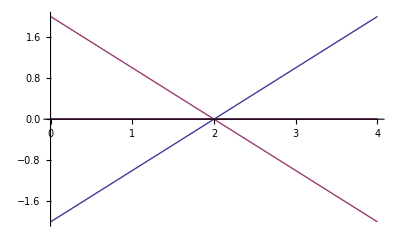

```mathematica
Subscript[p, 1]={-2,0,0};
Subscript[v, 1]={1,0,0};
r1=1;
Subscript[p, 2]={2,0,0};
Subscript[v, 2]={-1,0,0};
r2=1;
f=-(r1+r2)^2+Total[Subscript[p, 1]^2]+Total[Subscript[p, 2]^2]-2 Subscript[p, 1].Subscript[p, 2]+t (2 Subscript[p, 1].Subscript[v, 1]-2 Subscript[p, 2].Subscript[v, 1]-2 Subscript[p, 1].Subscript[v, 2]+2 Subscript[p, 2].Subscript[v, 2])+t^2 (Total[Subscript[v, 1]^2]+Total[Subscript[v, 2]^2]-2 Subscript[v, 1].Subscript[v, 2])==0
Solve[f,t]
Plot[{Subscript[p, 1]+Subscript[v, 1] t,Subscript[p, 2]+Subscript[v, 2] t},{t,0,4}]
```

```mathematica
Subscript[p, 1]={-2,0,0};
Subscript[v, 1]={1,0,0};
r1=0;
Subscript[p, 2]={2,0,0};
Subscript[v, 2]={-1,0,0};
r2=0;
f=-(r1+r2)^2+Total[Subscript[p, 1]^2]+Total[Subscript[p, 2]^2]-2 Subscript[p, 1].Subscript[p, 2]+t (2 Subscript[p, 1].Subscript[v, 1]-2 Subscript[p, 2].Subscript[v, 1]-2 Subscript[p, 1].Subscript[v, 2]+2 Subscript[p, 2].Subscript[v, 2])+t^2 (Total[Subscript[v, 1]^2]+Total[Subscript[v, 2]^2]-2 Subscript[v, 1].Subscript[v, 2])==0
Solve[f,t]
Plot[{Subscript[p, 1]+Subscript[v, 1] t,Subscript[p, 2]+Subscript[v, 2] t},{t,0,4}]
```

16-16 t+4 t^2==0

{{t→2},{t→2}}

-Graphics-

16-16 t+4 t^2==0

{{t→2},{t→2}}

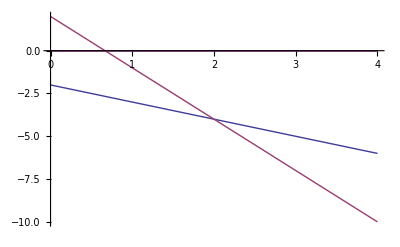

```mathematica
Subscript[p, 1]={-2,0,0};
Subscript[v, 1]={-1,0,0};
r1=0;
Subscript[p, 2]={2,0,0};
Subscript[v, 2]={-3,0,0};
r2=0;
f=-(r1+r2)^2+Total[Subscript[p, 1]^2]+Total[Subscript[p, 2]^2]-2 Subscript[p, 1].Subscript[p, 2]+t (2 Subscript[p, 1].Subscript[v, 1]-2 Subscript[p, 2].Subscript[v, 1]-2 Subscript[p, 1].Subscript[v, 2]+2 Subscript[p, 2].Subscript[v, 2])+t^2 (Total[Subscript[v, 1]^2]+Total[Subscript[v, 2]^2]-2 Subscript[v, 1].Subscript[v, 2])==0
Solve[f,t]
Plot[{Subscript[p, 1]+Subscript[v, 1] t,Subscript[p, 2]+Subscript[v, 2] t},{t,0,4}]
```

False

{}

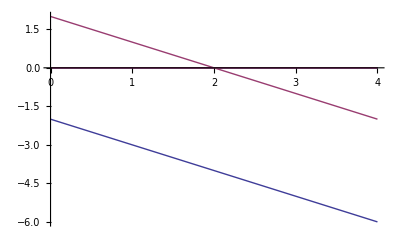

```mathematica
Subscript[p, 1]={-2,0,0};
Subscript[v, 1]={-1,0,0};
r1=0;
Subscript[p, 2]={2,0,0};
Subscript[v, 2]={-1,0,0};
r2=0;
f=-(r1+r2)^2+Total[Subscript[p, 1]^2]+Total[Subscript[p, 2]^2]-2 Subscript[p, 1].Subscript[p, 2]+t (2 Subscript[p, 1].Subscript[v, 1]-2 Subscript[p, 2].Subscript[v, 1]-2 Subscript[p, 1].Subscript[v, 2]+2 Subscript[p, 2].Subscript[v, 2])+t^2 (Total[Subscript[v, 1]^2]+Total[Subscript[v, 2]^2]-2 Subscript[v, 1].Subscript[v, 2])==0
Solve[f,t]
Plot[{Subscript[p, 1]+Subscript[v, 1] t,Subscript[p, 2]+Subscript[v, 2] t},{t,0,4}]
```

16+16 t+4 t^2==0

{{t→-2},{t→-2}}

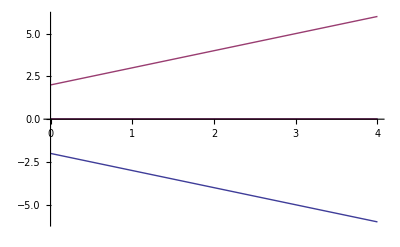

```mathematica
Subscript[p, 1]={-2,0,0};
Subscript[v, 1]={-1,0,0};
r1=0;
Subscript[p, 2]={2,0,0};
Subscript[v, 2]={1,0,0};
r2=0;
f=-(r1+r2)^2+Total[Subscript[p, 1]^2]+Total[Subscript[p, 2]^2]-2 Subscript[p, 1].Subscript[p, 2]+t (2 Subscript[p, 1].Subscript[v, 1]-2 Subscript[p, 2].Subscript[v, 1]-2 Subscript[p, 1].Subscript[v, 2]+2 Subscript[p, 2].Subscript[v, 2])+t^2 (Total[Subscript[v, 1]^2]+Total[Subscript[v, 2]^2]-2 Subscript[v, 1].Subscript[v, 2])==0
Solve[f,t]
Plot[{Subscript[p, 1]+Subscript[v, 1] t,Subscript[p, 2]+Subscript[v, 2] t},{t,0,4}]
```

```mathematica
Subscript[p, 1]={-1,0,0};
Subscript[u, 1]={1,0,0};
Subscript[r, 1]=1;
Subscript[p, 2]={1,0,0};
Subscript[u, 2]={0,0,0};
Subscript[r, 2]=1;
Solve[(√Total[((Subscript[p, 2]+Subscript[u, 2] t)-(Subscript[p, 1]+Subscript[u, 1] t))^2])^2==(Subscript[r, 1]+Subscript[r, 2])^2,t]
Subscript[np, 1]=Subscript[p, 1]+Subscript[u, 1] t
Subscript[np, 2]=Subscript[p, 2]+Subscript[u, 2] t
nml=Normalize[Subscript[np, 1]-Subscript[np, 2]];
Subscript[m, 1]=1;
Subscript[m, 2]=1;
Subscript[v, 1]=Subscript[u, 1]-(Subscript[u, 1].nml)nml+(Subscript[u, 1].nml)nml((Subscript[m, 1]-Subscript[m, 2])/(Subscript[m, 1]+Subscript[m, 2]))+(Subscript[u, 2].nml)nml(2 Subscript[m, 2]/(Subscript[m, 1]+Subscript[m, 2]))
Subscript[v, 2]=Subscript[u, 2]-(Subscript[u, 2].nml)nml+(Subscript[u, 2].nml)nml((Subscript[m, 2]-Subscript[m, 1])/(Subscript[m, 1]+Subscript[m, 2]))+(Subscript[u, 1].nml)nml(2 Subscript[m, 1]/(Subscript[m, 1]+Subscript[m, 2]))
```

{{t→0},{t→4}}

{-1+t,0,0}

{1,0,0}

{1-(-2+t)^2/Abs[-2+t]^2,0,0}

{(-2+t)^2/Abs[-2+t]^2,0,0}

```mathematica
(Subscript[m, 1] Subscript[u, 1]^2)/2+(Subscript[m, 2] Subscript[u, 2]^2)/2==(Subscript[m, 1] Subscript[v, 1]^2)/2+(Subscript[m, 2] Subscript[v, 2]^2)/2
```

{1/2,0,0}=={1/2 (1-(-2+t)^2/Abs[-2+t]^2)^2+(-2+t)^4/(2 Abs[-2+t]^4),0,0}

```mathematica
Subscript[v, 1]=(Subscript[m, 1]-Subscript[m, 2])/(Subscript[m, 1]+Subscript[m, 2])Subscript[u, 1]+(2 Subscript[m, 2])/(Subscript[m, 1]+Subscript[m, 2])Subscript[u, 2];
Subscript[v, 2]=(Subscript[m, 2]-Subscript[m, 1])/(Subscript[m, 1]+Subscript[m, 2])Subscript[u, 2]+(2 Subscript[m, 1])/(Subscript[m, 1]+Subscript[m, 2])Subscript[u, 1];

{Subscript[v, 1],Subscript[v, 2]}

Subscript[m, 1] Subscript[u, 1]+Subscript[m, 2] Subscript[u, 2]==Subscript[m, 1] Subscript[v, 1]+Subscript[m, 2] Subscript[v, 2]
```

{{0,0,0},{1,0,0}}

True